```mathematica
xi=8;
SigmaE=6.965;
SigmaB=5.59;
```

```mathematica
Clear[theta]
```

```mathematica
sol0=NDSolve[{Ap''[z]+(1-(2xi)/z)Ap[z]==-UnitStep[2xi-z] 1/(2z)(Sin[theta]^2/2(SigmaB Ap[z]-SigmaE Ap'[z]-SigmaB Am[z]-SigmaE Am'[z])+SigmaB Ap[z]-SigmaE Ap'[z]),
Am''[z]+(1+(2xi)/z)Am[z]==-UnitStep[2xi-z] 1/(2z)(Sin[theta]^2/2(SigmaB Ap[z]-SigmaE Ap'[z]-SigmaB Am[z]-SigmaE Am'[z])-SigmaB Am[z]-SigmaE Am'[z]),
Ap[100]==1/Sqrt[2],Ap'[100]==I/Sqrt[2],Am[100]==1/Sqrt[2],Am'[100]==I/Sqrt[2]}/.{theta->0},{Ap[z],Ap'[z],Am[z],Am'[z]},{z,100,0.01}][[1]];
sol45=NDSolve[{Ap''[z]+(1-(2xi)/z)Ap[z]==-UnitStep[2xi-z] 1/(2z)(Sin[theta]^2/2(SigmaB Ap[z]-SigmaE Ap'[z]-SigmaB Am[z]-SigmaE Am'[z])+SigmaB Ap[z]-SigmaE Ap'[z]),
Am''[z]+(1+(2xi)/z)Am[z]==-UnitStep[2xi-z] 1/(2z)(Sin[theta]^2/2(SigmaB Ap[z]-SigmaE Ap'[z]-SigmaB Am[z]-SigmaE Am'[z])-SigmaB Am[z]-SigmaE Am'[z]),
Ap[100]==1/Sqrt[2],Ap'[100]==I/Sqrt[2],Am[100]==1/Sqrt[2],Am'[100]==I/Sqrt[2]}/.{theta->π/4},{Ap[z],Ap'[z],Am[z],Am'[z]},{z,100,0.01}][[1]];
sol90=NDSolve[{Ap''[z]+(1-(2xi)/z)Ap[z]==-UnitStep[2xi-z] 1/(2z)(Sin[theta]^2/2(SigmaB Ap[z]-SigmaE Ap'[z]-SigmaB Am[z]-SigmaE Am'[z])+SigmaB Ap[z]-SigmaE Ap'[z]),
Am''[z]+(1+(2xi)/z)Am[z]==-UnitStep[2xi-z] 1/(2z)(Sin[theta]^2/2(SigmaB Ap[z]-SigmaE Ap'[z]-SigmaB Am[z]-SigmaE Am'[z])-SigmaB Am[z]-SigmaE Am'[z]),
Ap[100]==1/Sqrt[2],Ap'[100]==I/Sqrt[2],Am[100]==1/Sqrt[2],Am'[100]==I/Sqrt[2]}/.{theta->π/2},{Ap[z],Ap'[z],Am[z],Am'[z]},{z,100,0.01}][[1]];
```

```mathematica
Ep0sol[z_]=z^2 Ap'[z]/.sol0;
Bp0sol[z_]=z^2 Ap[z]/.sol0;
Em0sol[z_]=z^2 Am'[z]/.sol0;
Bm0sol[z_]=z^2 Am[z]/.sol0;
Ep45sol[z_]=z^2 Ap'[z]/.sol45;
Bp45sol[z_]=z^2 Ap[z]/.sol45;
Em45sol[z_]=z^2 Am'[z]/.sol45;
Bm45sol[z_]=z^2 Am[z]/.sol45;
Ep90sol[z_]=z^2 Ap'[z]/.sol90;
Bp90sol[z_]=z^2 Ap[z]/.sol90;
Em90sol[z_]=z^2 Am'[z]/.sol90;
Bm90sol[z_]=z^2 Am[z]/.sol90;
```

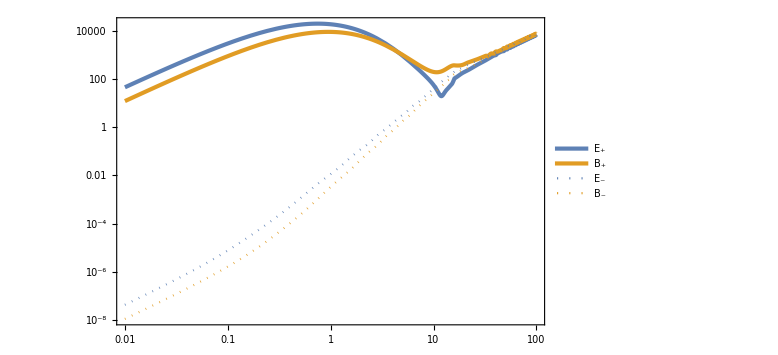

```mathematica
LogLogPlot[{Abs[Ep0sol[z]],Abs[Bp0sol[z]],Abs[Em0sol[z]],Abs[Bm0sol[z]]},{z,0.01,100},GridLines->{{2xi},None},PlotStyle->{AbsoluteThickness[3],AbsoluteThickness[3],{Color[1],Dotted},{Color[2],Dotted}},PlotLegends->Placed[LineLegend[{"E_+",SubPlus[B],"E_-",SubMinus[B]},LegendLayout->{"Column",2}],{0.75,0.2}]]
```

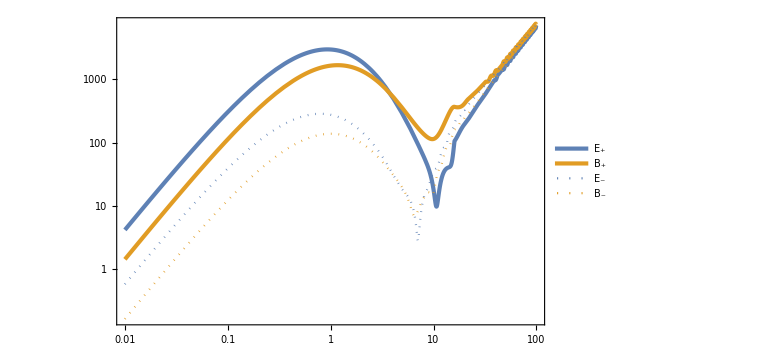

```mathematica
LogLogPlot[{Abs[Ep45sol[z]],Abs[Bp45sol[z]],Abs[Em45sol[z]],Abs[Bm45sol[z]]},{z,0.01,100},GridLines->{{2xi},None},PlotStyle->{AbsoluteThickness[3],AbsoluteThickness[3],{Color[1],Dotted},{Color[2],Dotted}},PlotLegends->Placed[LineLegend[{"E_+",SubPlus[B],"E_-",SubMinus[B]},LegendLayout->{"Column",2}],{0.75,0.2}]]
```

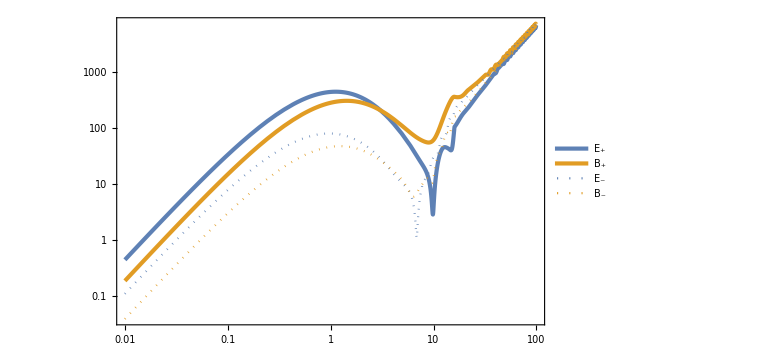

```mathematica
LogLogPlot[{Abs[Ep90sol[z]],Abs[Bp90sol[z]],Abs[Em90sol[z]],Abs[Bm90sol[z]]},{z,0.01,100},GridLines->{{2xi},None},PlotStyle->{AbsoluteThickness[3],AbsoluteThickness[3],{Color[1],Dotted},{Color[2],Dotted}},PlotLegends->Placed[LineLegend[{"E_+",SubPlus[B],"E_-",SubMinus[B]},LegendLayout->{"Column",2}],{0.75,0.2}]]
```

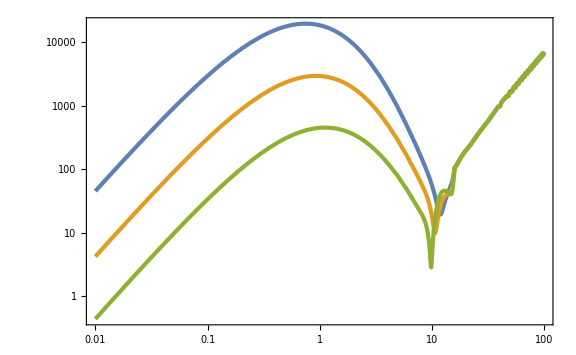

```mathematica
LogLogPlot[{Abs[Ep0sol[z]],Abs[Ep45sol[z]],Abs[Ep90sol[z]]},{z,0.01,100}]
```